# Изпит по Компютърни Числени Методи

## Борис Даскалов, 2001261020

## Задача 1

Дадено е уравнението x^2-30sin(x+3.14/(a+1))-(a+b) = 0, където a = 2 и b = 0
=> x^2-30sin(x+3.14/3)-2=0

## Да се намери общия брой на корените на уравнението

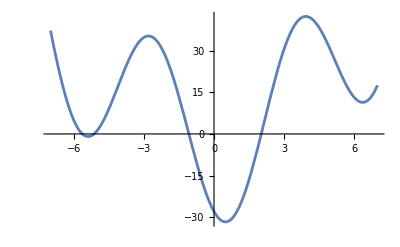

```mathematica
f[x_]:=x^2-30Sin[x+3.14/3]-2
Plot[f[x], {x,-7,7}]
```

### Първи корен

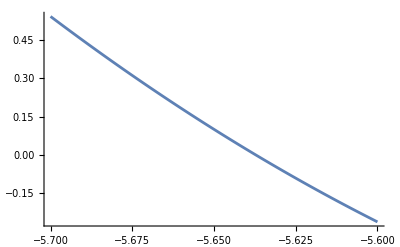

```mathematica
Plot[f[x], {x,-5.7,-5.6}]
```

```mathematica
f[-5.7]
```

0.542298

```mathematica
f[-5.6]
```

-0.261319

### Втори корен

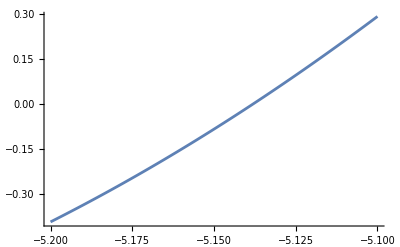

```mathematica
Plot[f[x], {x,-5.2,-5.1}]
```

```mathematica
f[-5.2]
```

-0.392691

```mathematica
f[-5.1]
```

0.292874

### Трети корен

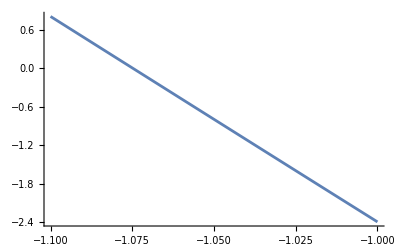

```mathematica
Plot[f[x], {x,-1.1,-1}]
```

```mathematica
f[-1.1]
```

0.809242

```mathematica
f[-1.]
```

-2.39949

### Четвърти корен

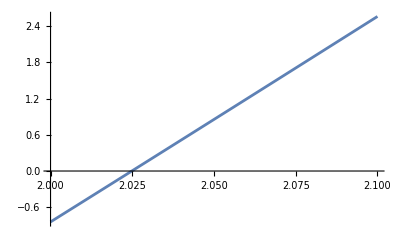

```mathematica
Plot[f[x], {x,2,2.1}]
```

```mathematica
f[2.]
```

-0.843505

```mathematica
f[2.1]
```

2.56222

Отговор: Общият брой на корените на уравнението е 4.
Първи корен (най-малък) - [-5.7,-5.6].
Втори корен - [-5.2,-5.1].
Трети корен - [-1.1,-1].
Четвърти корен (най-голям) - [2,2.1].

## Да се локализира най-големия реален корен в интервал [p,q]

```mathematica
Plot[f[x], {x,2,2.1}]
```

-Graphics-

```mathematica
f[2.]
```

-0.843505

```mathematica
f[2.1]
```

2.56222

Отговор: Най-големия реален корен се намира в интервал [2,2.1].

## Да се проверят условията за приложение на метода на Нютон

### Проверка на условията за сходимост на метода

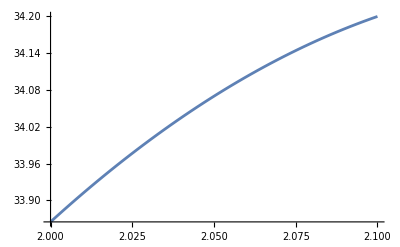

```mathematica
Plot[f'[x], {x, 2., 2.1}]
```

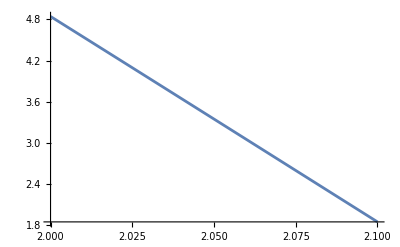

```mathematica
Plot[f''[x], {x, 2., 2.1}]
```

Извод: f’(x) и f’’(x) са с постоянни знаци в разглеждания интервал [2; 2.1], следователно методът на Нютон е сходящ.

### Определяне на начално приближение

f’’(x) > 0, следователно избираме x_0 така че f(x0) >0

```mathematica
x0=2.1
```

2.1

## Да се изчисли корена по метода на Нютон с точност 10^-4. Представете таблица с изчисленията.

```mathematica
f[x_]:=x^2-30Sin[x+3.14/3]-2
x0 = 2.1;
M2 = Abs[f''[2.1]];
m1 = Abs[f'[2.]];
P = M2/(2m1);
Print["n = ", 0, ", x = ", x0, ", f(TraditionalForm`", f[x0],
", f'(TraditionalForm`", f'[x0]]
epszad = 10^-4;
eps = 1;
For[n = 1, eps > epszad, n++,
x1 = x0 -f[x0]/f'[x0];
eps = P * Abs[x1-x0]^2 ;
x0 = x1;
Print["n = ", n, ", x = ", x0, ", f(TraditionalForm`", f[x0],
", f'(TraditionalForm`", f'[x0], ", ε_n = ", eps]
]
```

n = 0, x = 2.1, f(TraditionalForm`2.56222, f'(TraditionalForm`34.1996

n = 1, x = 2.02508, f(TraditionalForm`0.00728792, f'(TraditionalForm`33.977, ε_n = 0.00015313

n = 2, x = 2.02487, f(TraditionalForm`9.42205×10^-8, f'(TraditionalForm`33.9761, ε_n = 1.25518×10^-9

## Да се провери колко итерации биха били необходими, ако се използва метода на разполовяването в същия интервал [p,q] за същата стойност.

```mathematica
Log2[(2.1-2.)/10^-04] - 1
```

8.96578

Отговор: По метода на раполовяването биха били необходими 9 итерации за достигане на исканата
точност.

## Да се направи сравнение кой метод е по-ефективен за избрания интервал.

Отговор: По метода на раполовяването биха били необходими 9 итерации за достигане на исканата
точност.А по метода на Нютон бяха достатъчни 2 итерации. Следователно методът на Нютон
е по-ефективен.

## Задача 3

Да се състави таблицата (xi,f(xi)), къдетo xi = a + i(0.5), i = -5,5, f(x) = x - (b + 1) sin x, където а = 2 и b = 0
=> xi = 2 +i(0.5), i = -5,5, f(x) = x - 1sinx

## Генериране на данни (съставяне на табличната функция)

```mathematica
xt = Table[2+i*0.1,{i,-5,5}]
```

{1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5}

```mathematica
f[x_] := x - 1Sin[x]
```

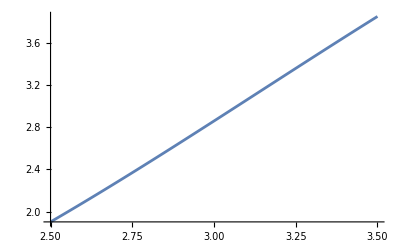

```mathematica
Plot[f[x], {x, 2.5, 3.5}]
```

## Избирам точките 1.9,2.,2.1,2.2

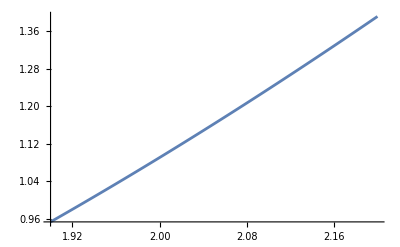

```mathematica
grf=Plot[f[x],{x,1.9,2.2}];
grp = ListPlot[points, PlotStyle->Black];
Show[grf, grp]
```

```mathematica
points
```

{{0.5,2.},{0.525,2.00099},{0.55,1.99981},{0.575,1.99645},{0.6,1.99088},{0.625,1.98308},{0.65,1.97302},{0.675,1.9607},{0.7,1.94609},{0.725,1.92917},{0.75,1.90993},{0.775,1.88835},{0.8,1.86441},{0.825,1.83811},{0.85,1.80942},{0.875,1.77833},{0.9,1.74484},{0.925,1.70892},{0.95,1.67057},{0.975,1.62978},{1.,1.58654},{1.025,1.54083}}

## Задача 4

Дадена е началната задача за ОДУ:
y’ = y - (2 + a)sinx, y(b) = a + b, x ∈ [b, b + 0.5] където a = 2 и b = 0;
=> y’ = y - 4sinx, y(0) = 2, x ∈ [0, 0.5]

## Да се намери точното решение на задачата

### Търсим точно решение

```mathematica
Clear[x,y]
DSolve[{y'[x]==y[x]-(2+2) Sin[x],y[0]==2},y[x],x]
```

{{y[x]→2 (Cos[x]+Sin[x])}}

### Визуализация на точно решение

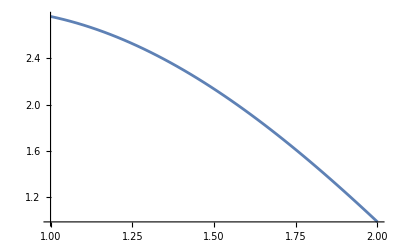

```mathematica
yt[x_]:=2 (Cos[x]+Sin[x])
Plot[yt[x],{x,1,2}]
```

## По метод на Рунге-Кута (1,1) да се реши приближено задачата със стъпка 0.025. Запишете резултатите в таблица. Сравнете с точното решение.

Мрежата е с n = 20. и стъпка h = 0.025

Теоретичната локална  грешка е 0.000015625

Теоретичната глобална грешка е 0.000625

i = 0, x_i = 0.5, y_i = 2., k1 = 0.00205745, k2 = -0.0000698643, y_точно = 2.71402, Истинска грешка = 0.714016

i = 1, x_i = 0.525, y_i = 2.00099, k1 = -0.0000964557, k2 = -0.00224629, y_точно = 2.73307, Истинска грешка = 0.73208

i = 2, x_i = 0.55, y_i = 1.99982, k1 = -0.00227316, k2 = -0.00444475, y_точно = 2.75042, Истинска грешка = 0.750601

i = 3, x_i = 0.575, y_i = 1.99646, k1 = -0.00447189, k2 = -0.00666446, y_точно = 2.76605, Истинска грешка = 0.769591

i = 4, x_i = 0.6, y_i = 1.9909, k1 = -0.00669187, k2 = -0.00890464, y_точно = 2.77996, Истинска грешка = 0.789061

i = 5, x_i = 0.625, y_i = 1.9831, k1 = -0.0089323, k2 = -0.0111645, y_точно = 2.79212, Истинска грешка = 0.809024

i = 6, x_i = 0.65, y_i = 1.97305, k1 = -0.0111924, k2 = -0.0134433, y_точно = 2.80254, Истинска грешка = 0.829492

i = 7, x_i = 0.675, y_i = 1.96073, k1 = -0.0134715, k2 = -0.0157403, y_точно = 2.81121, Истинска грешка = 0.850478

i = 8, x_i = 0.7, y_i = 1.94612, k1 = -0.0157686, k2 = -0.0180546, y_точно = 2.81812, Истинска грешка = 0.871995

i = 9, x_i = 0.725, y_i = 1.92921, k1 = -0.0180832, k2 = -0.0203856, y_точно = 2.82327, Истинска грешка = 0.894057

i = 10, x_i = 0.75, y_i = 1.90998, k1 = -0.0204144, k2 = -0.0227325, y_точно = 2.82666, Истинска грешка = 0.916676

i = 11, x_i = 0.775, y_i = 1.88841, k1 = -0.0227615, k2 = -0.0250945, y_точно = 2.82827, Истинска грешка = 0.939869

i = 12, x_i = 0.8, y_i = 1.86448, k1 = -0.0251237, k2 = -0.0274709, y_точно = 2.82813, Истинска грешка = 0.963648

i = 13, x_i = 0.825, y_i = 1.83818, k1 = -0.0275003, k2 = -0.029861, y_точно = 2.82621, Истинска грешка = 0.988029

i = 14, x_i = 0.85, y_i = 1.8095, k1 = -0.0298906, k2 = -0.0322641, y_точно = 2.82253, Истинска грешка = 1.01303

i = 15, x_i = 0.875, y_i = 1.77842, k1 = -0.0322938, k2 = -0.0346795, y_точно = 2.81708, Истинска грешка = 1.03866

i = 16, x_i = 0.9, y_i = 1.74494, k1 = -0.0347093, k2 = -0.0371064, y_точно = 2.80987, Истинска грешка = 1.06494

i = 17, x_i = 0.925, y_i = 1.70903, k1 = -0.0371364, k2 = -0.0395443, y_точно = 2.80091, Истинска грешка = 1.09188

i = 18, x_i = 0.95, y_i = 1.67069, k1 = -0.0395744, k2 = -0.0419924, y_точно = 2.7902, Истинска грешка = 1.11951

i = 19, x_i = 0.975, y_i = 1.6299, k1 = -0.0420226, k2 = -0.0444501, y_точно = 2.77774, Истинска грешка = 1.14784

i = 20, x_i = 1., y_i = 1.58667, k1 = -0.0444804, k2 = -0.0469167, y_точно = 2.76355, Истинска грешка = 1.17688

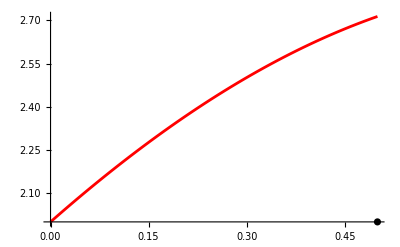

```mathematica
(*Въвеждаме условието на задачата*)
a = 0.;b=0.5;
x = b;
y = 2.;
points = {{x,y}};
f[x_,y_] := y-(2+2)Sin[x]

(*Точно решение*)
yt[x_] := 2 (Cos[x]+Sin[x])
(*Съставяме мрежата*)
h = 0.025; n= (b-a)/h;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]

(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]

(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1=h*f[x,y];
k2=h*f[x+h,y+k1];
Print["i = ", i, ", x_i = ",x, ", y_i = ",y, ", k1 = ",k1,", k2 = ",k2,", y_(:0442:043e:0447:043d:043e) = ", yt[x], ", Истинска грешка = ", Abs[y-yt[x]]];
y = y+1/2(k1+k2);
x=x+h;
AppendTo[points,{x,y}]
]

(*Визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

## Каква би била точността при използване на модифицирания метод на Ойлер за поставнеата задача със същата стъпка? Направете сравнени между двата метода.

```mathematica
(*Въвеждаме условието на задачата*)
a = 0.;b=0.5;
x = b;
y = 2.;
points = {{x,y}};
f[x_,y_] := y-(2+2)Sin[x]

(*Точно решение*)
yt[x_] := 2 (Cos[x]+Sin[x])

(*Съставяме мрежата*)
n = 20; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]

(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^2]
Print["Теоретичната глобална грешка е ", h]

(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
x12 = x + h/2;
y12 = y + h/2 f[x,y];
Print["i = ", i, ", x_i = ", x, ", y_i = ", y, ", f_i = ", f[x,y]  , ", x_(i + 1/2) = ", x12, ", y_(i + 1/2) = ", y12, ", f_(i + 1/2) = ", f[x12,y12]  ", y_(:0442:043e:0447:043d:043e) = ", yt[x], ", Истинска грешка = ", Abs[y-yt[x]]];
y = y + h*f[x12,y12];
x = x + h;
AppendTo[points, {x,y}]
]

(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a, b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt, grp]
```

Мрежата е с n = 20 и стъпка h = 0.025

Теоретичната локална грешка  е 0.000625

Теоретичната глобална грешка е 0.025

i = 0, x_i = 0.5, y_i = 2., f_i = 0.0822978, x_(i + 1/2) = 0.5125, y_(i + 1/2) = 2.00103, f_(i + 1/2) = 0.0395984 , y_точно = 2.71402, Истинска грешка = 0.714016

i = 1, x_i = 0.525, y_i = 2.00099, f_i = -0.00386206, x_(i + 1/2) = 0.5375, y_(i + 1/2) = 2.00094, f_(i + 1/2) = -0.0470188 , y_точно = 2.73307, Истинска грешка = 0.732084

i = 2, x_i = 0.55, y_i = 1.99981, f_i = -0.0909344, x_(i + 1/2) = 0.5625, y_(i + 1/2) = 1.99868, f_(i + 1/2) = -0.134533 , y_точно = 2.75042, Истинска грешка = 0.750609

i = 3, x_i = 0.575, y_i = 1.99645, f_i = -0.178888, x_(i + 1/2) = 0.5875, y_(i + 1/2) = 1.99422, f_(i + 1/2) = -0.222913 , y_точно = 2.76605, Истинска грешка = 0.769603

i = 4, x_i = 0.6, y_i = 1.99088, f_i = -0.267692, x_(i + 1/2) = 0.6125, y_(i + 1/2) = 1.98753, f_(i + 1/2) = -0.312127 , y_точно = 2.77996, Истинска грешка = 0.789078

i = 5, x_i = 0.625, y_i = 1.98308, f_i = -0.357314, x_(i + 1/2) = 0.6375, y_(i + 1/2) = 1.97861, f_(i + 1/2) = -0.402145 , y_точно = 2.79212, Истинска грешка = 0.809046

i = 6, x_i = 0.65, y_i = 1.97302, f_i = -0.447724, x_(i + 1/2) = 0.6625, y_(i + 1/2) = 1.96743, f_(i + 1/2) = -0.492935 , y_точно = 2.80254, Истинска грешка = 0.829519

i = 7, x_i = 0.675, y_i = 1.9607, f_i = -0.538891, x_(i + 1/2) = 0.6875, y_(i + 1/2) = 1.95396, f_(i + 1/2) = -0.584466 , y_точно = 2.81121, Истинска грешка = 0.85051

i = 8, x_i = 0.7, y_i = 1.94609, f_i = -0.630784, x_(i + 1/2) = 0.7125, y_(i + 1/2) = 1.9382, f_(i + 1/2) = -0.676709 , y_точно = 2.81812, Истинска грешка = 0.872033

i = 9, x_i = 0.725, y_i = 1.92917, f_i = -0.723373, x_(i + 1/2) = 0.7375, y_(i + 1/2) = 1.92013, f_(i + 1/2) = -0.769632 , y_точно = 2.82327, Истинска грешка = 0.894101

i = 10, x_i = 0.75, y_i = 1.90993, f_i = -0.816627, x_(i + 1/2) = 0.7625, y_(i + 1/2) = 1.89972, f_(i + 1/2) = -0.863205 , y_точно = 2.82666, Истинска грешка = 0.916727

i = 11, x_i = 0.775, y_i = 1.88835, f_i = -0.910516, x_(i + 1/2) = 0.7875, y_(i + 1/2) = 1.87697, f_(i + 1/2) = -0.957399 , y_точно = 2.82827, Истинска грешка = 0.939926

i = 12, x_i = 0.8, y_i = 1.86441, f_i = -1.00501, x_(i + 1/2) = 0.8125, y_(i + 1/2) = 1.85185, f_(i + 1/2) = -1.05218 , y_точно = 2.82813, Истинска грешка = 0.963713

i = 13, x_i = 0.825, y_i = 1.83811, f_i = -1.10008, x_(i + 1/2) = 0.8375, y_(i + 1/2) = 1.82436, f_(i + 1/2) = -1.14753 , y_точно = 2.82621, Истинска грешка = 0.988101

i = 14, x_i = 0.85, y_i = 1.80942, f_i = -1.1957, x_(i + 1/2) = 0.8625, y_(i + 1/2) = 1.79447, f_(i + 1/2) = -1.24341 , y_точно = 2.82253, Истинска грешка = 1.01311

i = 15, x_i = 0.875, y_i = 1.77833, f_i = -1.29184, x_(i + 1/2) = 0.8875, y_(i + 1/2) = 1.76219, f_(i + 1/2) = -1.3398 , y_точно = 2.81708, Истинска грешка = 1.03875

i = 16, x_i = 0.9, y_i = 1.74484, f_i = -1.38847, x_(i + 1/2) = 0.9125, y_(i + 1/2) = 1.72748, f_(i + 1/2) = -1.43666 , y_точно = 2.80987, Истинска грешка = 1.06503

i = 17, x_i = 0.925, y_i = 1.70892, f_i = -1.48556, x_(i + 1/2) = 0.9375, y_(i + 1/2) = 1.69035, f_(i + 1/2) = -1.53397 , y_точно = 2.80091, Истинска грешка = 1.09199

i = 18, x_i = 0.95, y_i = 1.67057, f_i = -1.58309, x_(i + 1/2) = 0.9625, y_(i + 1/2) = 1.65079, f_(i + 1/2) = -1.63171 , y_точно = 2.7902, Истинска грешка = 1.11962

i = 19, x_i = 0.975, y_i = 1.62978, f_i = -1.68103, x_(i + 1/2) = 0.9875, y_(i + 1/2) = 1.60877, f_(i + 1/2) = -1.72984 , y_точно = 2.77774, Истинска грешка = 1.14796

i = 20, x_i = 1., y_i = 1.58654, f_i = -1.77935, x_(i + 1/2) = 1.0125, y_(i + 1/2) = 1.56429, f_(i + 1/2) = -1.82834 , y_точно = 2.76355, Истинска грешка = 1.17701

-Graphics-